## CellOutwardVector-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 11:53:58
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 8 cells in the tissue.

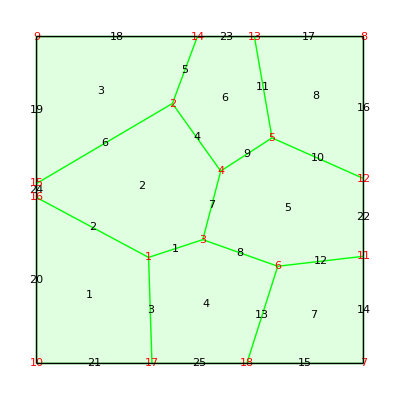

```mathematica
q=TemplateRandomSquareGrid[9, {-50, -50}, {50, 50}];
Q=Tissue2DTissue[q]; 
Print["There are ", NTissueCells[Q], " cells in the tissue."];  
ShowTissue[Q, "CellNumbers"-> True, Frame-> False, "EdgeStyles"-> Directive[Green,Thick], "EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

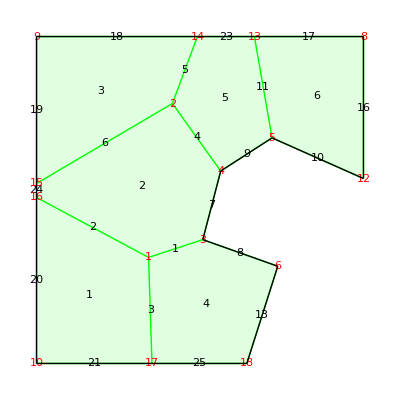

```mathematica
R=DeleteCell[Q, 5];
R=DeleteCell[R, 7];
S=DTissue2Tissue[R];
map=ShowTissue[S, "CellNumbers"-> True, "EdgeStyles"-> Directive[Green,Thick],"EdgeNumbers"-> True, "VertexNumbers"-> Directive[Red,FontSize-> 12]]
```

## Find the outward vectors from each vertex in cell 4

```mathematica
CellVertexNumbers[S,4]
```

{17,18,6,3,1}

```mathematica
COV=CellOutwardVector[S,4,#]&/@CellVertexNumbers[S,4]
```

{{-0.674665,-0.738124},{0.562122,-0.827054},{0.884306,0.466908},{-0.0551418,0.998479},{-0.778816,0.627253}}

```mathematica
CVC=CellVertexCoordinates[S,4]
```

{{-14.693,-50.},{14.321,-50.},{23.7854,-20.2641},{0.860968,-12.1243},{-15.7277,-17.5592}}

#### figure out a good number for the length of the vector

```mathematica
len = .5 * EdgeLengths[S]//Mean
```

15.3728

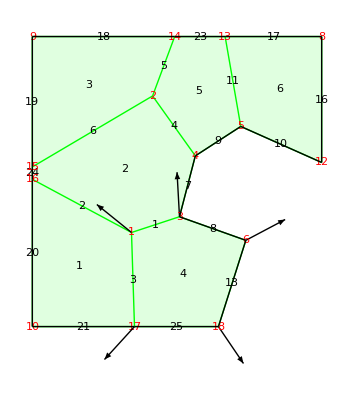

```mathematica
Show[map,Graphics[MapThread[Arrow[{#1,#1+len*#2}]&, {CVC, COV}]]]
```